```mathematica
(* This code is structured so that we first get theoretical optimal input distributions for concentrations of ACh and glutamate, and then compare them to experiment. *)
```

```mathematica
(* From a two-state, two-binding site statistical mechanical model, we have the probability of open being *)
```

```mathematica
popenHill[c_,Kd_,nH_]:=c^nH/(c^nH+Kd^nH)
```

```mathematica
(* Cholinergic NMJs: Optimal input distribution for ACh *)
(* Adult nACh receptors have a Hill probability of being open given in Prince and Sine, Journal of Biological Chemistry 1999. There were parameters given for an MWC model, but the resulting popen curve did not, upon inspection by eye, match the data. *)
popenAdultnAChR[c_]:=popenHill[c,1.5*10^-6,1.3]
```

```mathematica
(* Fetal nACh receptors have a statistical mechanical probability of being open that we fit to data from Prince and Sine, Journal of Biological Chemistry 1999. *)
```

```mathematica
popenFetalnAChR[c_]:=popenHill[c,1.3*10^-6,1.4]
```

```mathematica
(* This plot compares the popen of adult and fetal nAChR ion channels using the data from Prince and Sine, Journal of Biological Chemistry 1999. It shows that there is a slight shift in the responses of these ion channels during development. *)
```

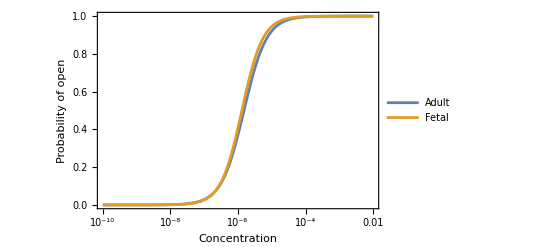

```mathematica
LogLinearPlot[{popenAdultnAChR[c],popenFetalnAChR[c]},{c,10^-10,10^-2},PlotLegends->Placed[{"Adult","Fetal"},{Right,Bottom}],FrameLabel->{"Concentration","Probability of open"},Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}]
```

```mathematica
(* The optimal input distribution of ACh comes from the binomial distribution which limits to a Gaussian distribution in the large N limit *)
```

```mathematica
ZAdultACh=Integrate[1/Sqrt[p*(1-p)],{p,popenAdultnAChR[0],Limit[popenAdultnAChR[c],c->Infinity]}]
```

3.14159

```mathematica
poptimalAdultACh[c_]:=D[popenAdultnAChR[x],x]/.x->c/Sqrt[popenAdultnAChR[c]*(1-popenAdultnAChR[c])]/ZAdultACh
```

```mathematica
ZFetalACh=Integrate[1/Sqrt[p*(1-p)],{p,popenFetalnAChR[0],Limit[popenFetalnAChR[c],c->Infinity]}]
```

3.14159

```mathematica
poptimalFetalACh[c_]:=D[popenFetalnAChR[x],x]/.x->c/Sqrt[popenFetalnAChR[c]*(1-popenFetalnAChR[c])]/ZFetalACh
```

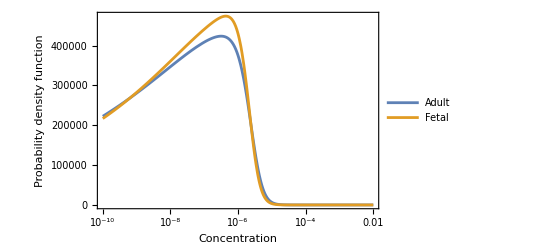

```mathematica
LogLinearPlot[{poptimalAdultACh[c],poptimalFetalACh[c]},{c,10^-10,10^-2},PlotLegends->Placed[{"Adult","Fetal"},{Right,Top}],FrameLabel->{"Concentration","Probability density function"},Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}]
```

```mathematica
CapacityAdultACh[n_]:=0.5*Log2[n]+Log2[ZAdultACh]-0.5*Log2[2*Pi*Exp[1]]
```

```mathematica
CapacityFetalACh[n_]:=0.5*Log2[n]+Log2[ZFetalACh]-0.5*Log2[2*Pi*Exp[1]]
```

```mathematica
(* Glutamatergic optimal input distribution is different! *)
```

```mathematica
popenGlu1[c_]:=c^1.6/(c^1.6+(3.4*10^-3)^1.6)
```

```mathematica
popenGlu2[c_]:=c^1.5/(c^1.5+(5.9*10^-3)^1.5)
```

```mathematica
meanpGlu[c_]:=0.7*5.8*popenGlu1[c]+0.3*2.0*popenGlu2[c]
```

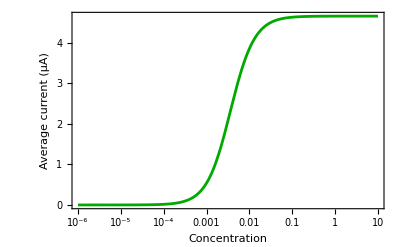

```mathematica
LogLinearPlot[meanpGlu[c],{c,10^-6,10},FrameLabel->{"Concentration","Average current (μA)"},Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14},PlotStyle->Darker[Green]]
```

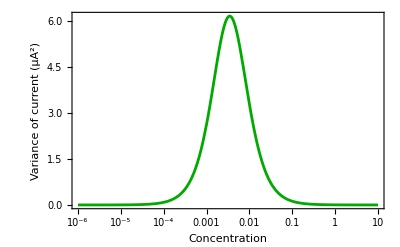

```mathematica
LogLinearPlot[varpGlu[c],{c,10^-6,10},FrameLabel->{"Concentration","Variance of current (µA^2)"},Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14},PlotStyle->Darker[Green]]
```

```mathematica
varpGlu[c_]:=0.7*5.8^2*popenGlu1[c]*(1-popenGlu1[c])+0.3*2.0^2*popenGlu2[c]*(1-popenGlu2[c])
```

```mathematica
ZGlu=NIntegrate[(D[meanpGlu[x],x]/.x->c)/Sqrt[varpGlu[c]],{c,0,Infinity}]
```

2.98767

```mathematica
poptimalGlu[c_]:=(D[meanpGlu[x],x]/.x->c)/Sqrt[varpGlu[c]]/ZGlu
```

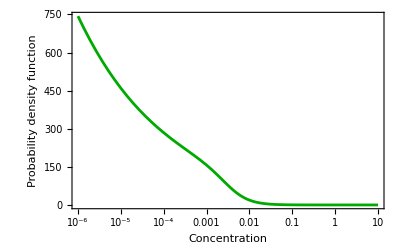

```mathematica
LogLinearPlot[poptimalGlu[c],{c,10^-6,10},FrameLabel->{"Concentration","Probability density function"},Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14},PlotStyle->Darker[Green]]
```

```mathematica
CapacityGlu[n_]:=0.5*Log2[n]+Log2[ZGlu]-0.5*Log2[2*Pi*Exp[1]]
```

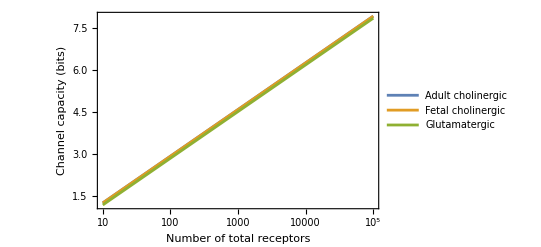

```mathematica
LogLinearPlot[{CapacityAdultACh[n],CapacityFetalACh[n],CapacityGlu[n]},{n,10,100000},Frame->True,FrameLabel->{"Number of total receptors","Channel capacity (bits)"},PlotLegends->Placed[{"Adult cholinergic","Fetal cholinergic","Glutamatergic"},{Left,Top}],PlotRange->All,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}]
```

```mathematica
Plot3D[Log2[Sqrt[2/Pi/Exp[1]]*(ArcSin[x]-ArcSin[y])],{x,0,1},{y,0,1},AxesLabel->{DisplayForm[SubsuperscriptBox["p","open","max"]],DisplayForm[SubsuperscriptBox["p","open","min"]],"Contribution to C"},LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}]
```

-Graphics3D-

```mathematica
(* Let's compare all three optimal input distributions against each other with a conversion to synaptic vesicle release probabilities *)
```

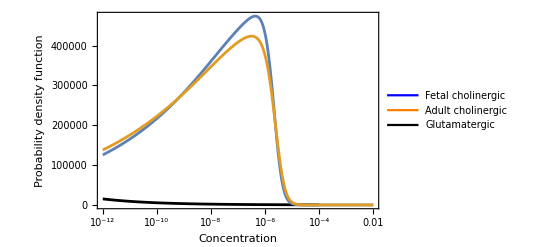

```mathematica
Legended[Show[LogLinearPlot[{poptimalGlu[c]},{c,10^-12,10^-4},PlotStyle->Black],LogLinearPlot[{poptimalFetalACh[c],poptimalAdultACh[c]},{c,10^-12,10^-2}],PlotRange->All,FrameLabel->{"Concentration","Probability density function"},Frame->True],Placed[LineLegend[{Blue,Orange,Black},{"Fetal cholinergic","Adult cholinergic","Glutamatergic"}],{Right,Top}]]
```

```mathematica
(* Now to compare to experiment, we have to rescale the probability of synaptic vesicle release into a concentration, at least in order of magnitude. *)
```

```mathematica
cs={0.02,0.07111111,0.1744444,0.222222222,0.4,0.4315217764}*50*5000/(6.022*10^23*2.78*10^-15);
```

```mathematica
pexp={172.555556,157.6460905,34.49176955,22.9218107,6.903292181,3.3333333,1.74089}/399.593;
```

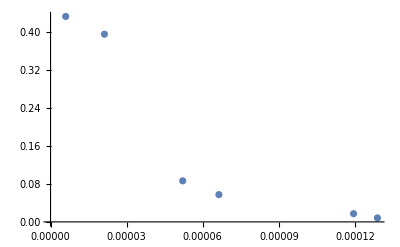

```mathematica
ListPlot[Table[{cs[[i]],pexp[[i]]},{i,1,6}]]
```

```mathematica
csAugment={0,0.5*(0.02+0.07111111),0.5*(0.07111111+0.1744444),0.5*(0.1744444+0.222222222),0.5*(0.222222222+0.4),0.5*(0.4+0.4315217764),Infinity}*50*5000/(6.022*10^23*2.78*10^-15);
```

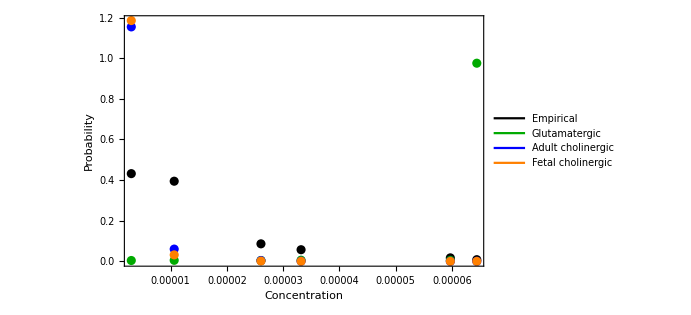

```mathematica
Legended[Show[ListPlot[Table[{cs[[i]],pexp[[i]]},{i,1,6}],PlotStyle->Black],ListPlot[Table[{cs[[i]],NIntegrate[poptimalGlu[c],{c,csAugment[[i]],csAugment[[i+1]]}]},{i,1,6}],PlotStyle->Darker[Green]],ListPlot[Table[{cs[[i]],NIntegrate[poptimalAdultACh[c],{c,csAugment[[i]],csAugment[[i+1]]}]},{i,1,6}],PlotStyle->Blue],ListPlot[Table[{cs[[i]],NIntegrate[poptimalFetalACh[c],{c,csAugment[[i]],csAugment[[i+1]]}]},{i,1,6}],PlotStyle->Orange],FrameLabel->{"Concentration","Probability"},PlotRange->All,Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}],Placed[LineLegend[{Black,Darker[Green],Blue,Orange},{"Empirical","Glutamatergic","Adult cholinergic","Fetal cholinergic"},LabelStyle->Directive[FontSize->14]],{Right,Top}]]
```

```mathematica
Legended[Show[ListPlot[Table[{cs[[i]],pexp[[i]]},{i,1,6}],Joined->True,PlotStyle->Blue],ListPlot[Table[{cs[[i]],NIntegrate[poptimalGlu[c],{c,csAugment[[i]],csAugment[[i+1]]}]},{i,1,6}],Joined->True,PlotStyle->Black],ListPlot[Table[{cs[[i]],NIntegrate[poptimalAdultACh[c],{c,csAugment[[i]],csAugment[[i+1]]}]},{i,1,6}],Joined->True,PlotStyle->Orange],ListPlot[Table[{cs[[i]],NIntegrate[poptimalFetalACh[c],{c,csAugment[[i]],csAugment[[i+1]]}]},{i,1,6}],Joined->True,PlotStyle->Red],FrameLabel->{"Concentration","Probability"},PlotRange->All,Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}],Placed[LineLegend[{Blue,Black,Orange,Red},{"Empirical","Glutamatergic","Adult cholinergic","Fetal cholinergic"},LabelStyle->Directive[FontSize->14]],{Right,Top}]]
```

```mathematica
(* For the Appendix, we show that membrane voltage matters a bit. *)
```

```mathematica
popenHill2[c_,Kd_,nH_,F_]:=F*c^nH/(F*c^nH+Kd^nH)
```

```mathematica
F=1.2117;
```

```mathematica
popenAdultnAChR2[c_]:=popenHill2[c,1.5*10^-6,1.3,F]
```

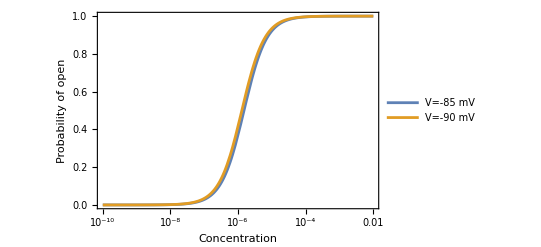

```mathematica
LogLinearPlot[{popenAdultnAChR[c],popenAdultnAChR2[c]},{c,10^-10,10^-2},PlotLegends->Placed[{"V=-85 mV","V=-90 mV"},{Right,Bottom}],FrameLabel->{"Concentration","Probability of open"},Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}]
```

```mathematica
ZAdultACh2=Integrate[1/Sqrt[p*(1-p)],{p,popenAdultnAChR2[0],Limit[popenAdultnAChR2[c],c->Infinity]}]
```

3.14159-7.94136×10^-9 ⅈ

```mathematica
poptimalAdultACh2[c_]:=D[popenAdultnAChR2[x],x]/.x->c/Sqrt[popenAdultnAChR2[c]*(1-popenAdultnAChR2[c])]/ZAdultACh2
```

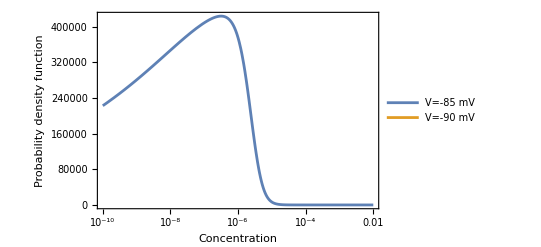

```mathematica
LogLinearPlot[{poptimalAdultACh[c],poptimalAdultACh2[c]},{c,10^-10,10^-2},PlotLegends->Placed[{"V=-85 mV","V=-90 mV"},{Right,Top}],FrameLabel->{"Concentration","Probability density function"},Frame->True,LabelStyle->Directive[FontSize->16,FontFamily->"Arial"],BaseStyle->{FontSize->14}]
```